# Potential for noble gases molecules

Authors:

School of Physical Sciences and Nanotechnology

In this notebook we will compute the interaction between two noble atoms:

```mathematica
SetDirectory["/home/angeldavid/wrk/session1"];
```

```mathematica
Range[2.4,7.0,0.05]//Map[ToString[NumberForm[#,{4,2}]]<>" "&,#]&//StringJoin
```

2.40 2.45 2.50 2.55 2.60 2.65 2.70 2.75 2.80 2.85 2.90 2.95 3.00 3.05 3.10 3.15 3.20 3.25 3.30 3.35 3.40 3.45 3.50 3.55 3.60 3.65 3.70 3.75 3.80 3.85 3.90 3.95 4.00 4.05 4.10 4.15 4.20 4.25 4.30 4.35 4.40 4.45 4.50 4.55 4.60 4.65 4.70 4.75 4.80 4.85 4.90 4.95 5.00 5.05 5.10 5.15 5.20 5.25 5.30 5.35 5.40 5.45 5.50 5.55 5.60 5.65 5.70 5.75 5.80 5.85 5.90 5.95 6.00 6.05 6.10 6.15 6.20 6.25 6.30 6.35 6.40 6.45 6.50 6.55 6.60 6.65 6.70 6.75 6.80 6.85 6.90 6.95 7.00

## He_2

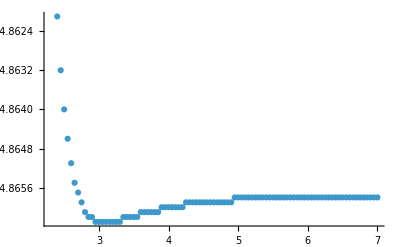

```mathematica
atom = "He";
file = "results-"<>atom<>".dat";
data[atom]=Import[file];
ListPlot[data[atom][[1;;-2]],PlotRange->All]
```

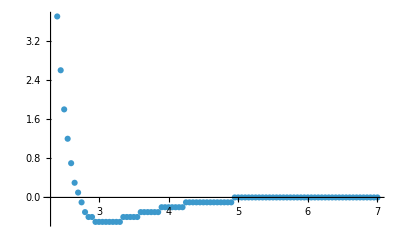

```mathematica
dataNEW[atom]=data[atom][[1;;-2]]//Map[(#-{0,data[atom][[-1,2]]}){1,10^3}&,#]&;
dataNEW[atom]//ListPlot[#,PlotRange->All]&
```

## Ne_2

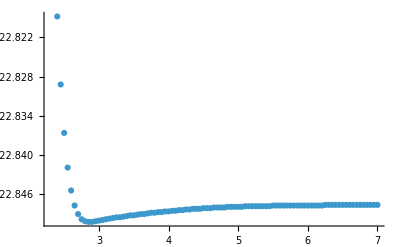

```mathematica
atom = "Ne";
file = "results-"<>atom<>".dat";
data[atom]=Import[file];
ListPlot[data[atom][[1;;-2]],PlotRange->All]
```

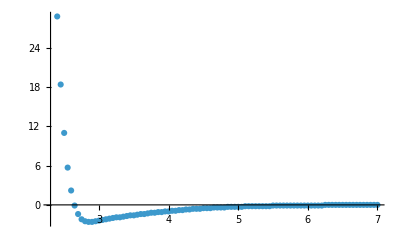

```mathematica
dataNEW[atom]=data[atom][[1;;-2]]//Map[(#-{0,data[atom][[-1,2]]}){1,10^3}&,#]&;
dataNEW[atom]//ListPlot[#,PlotRange->All]&
```

```mathematica
LJm = 4 ϵ ((a/x)^12-(a/x)^6)  ;
```

```mathematica
nlmLJ = NonlinearModelFit[dataNEW[atom],LJm,{a,ϵ},x,MaxIterations->Infinity]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[…]

```mathematica
nlmLJ[x]
```

-1.09855×10^12 ((3.02167×10^-18)/x^12-(1.7383×10^-9)/x^6)

```mathematica
nlmLJ["RSquared"]
```

0.342408

```mathematica
nlmLJ["BestFitParameters"]
```

{a→0.0346753,ϵ→-2.74637×10^11}

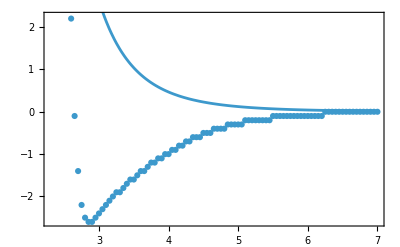

```mathematica
Show[ListPlot[dataNEW[atom]],Plot[nlm[x],{x,0,7}],Frame->True]
```

We can see that it is not a good model

```mathematica
dataNEW2[atom]=dataNEW[atom][[7;;-1]]
```

{{2.7,-1.4},{2.75,-2.2},{2.8,-2.5},{2.85,-2.6},{2.9,-2.6},{2.95,-2.5},{3.,-2.4},{3.05,-2.3},{3.1,-2.2},{3.15,-2.1},{3.2,-2.},{3.25,-1.9},{3.3,-1.9},{3.35,-1.8},{3.4,-1.7},{3.45,-1.6},{3.5,-1.6},{3.55,-1.5},{3.6,-1.4},{3.65,-1.4},{3.7,-1.3},{3.75,-1.2},{3.8,-1.2},{3.85,-1.1},{3.9,-1.1},{3.95,-1.},{4.,-1.},{4.05,-0.9},{4.1,-0.9},{4.15,-0.8},{4.2,-0.8},{4.25,-0.7},{4.3,-0.7},{4.35,-0.6},{4.4,-0.6},{4.45,-0.6},{4.5,-0.5},{4.55,-0.5},{4.6,-0.5},{4.65,-0.4},{4.7,-0.4},{4.75,-0.4},{4.8,-0.4},{4.85,-0.3},{4.9,-0.3},{4.95,-0.3},{5.,-0.3},{5.05,-0.3},{5.1,-0.2},{5.15,-0.2},{5.2,-0.2},{5.25,-0.2},{5.3,-0.2},{5.35,-0.2},{5.4,-0.2},{5.45,-0.2},{5.5,-0.1},{5.55,-0.1},{5.6,-0.1},{5.65,-0.1},{5.7,-0.1},{5.75,-0.1},{5.8,-0.1},{5.85,-0.1},{5.9,-0.1},{5.95,-0.1},{6.,-0.1},{6.05,-0.1},{6.1,-0.1},{6.15,-0.1},{6.2,-0.1},{6.25,0.},{6.3,0.},{6.35,0.},{6.4,0.},{6.45,0.},{6.5,0.},{6.55,0.},{6.6,0.},{6.65,0.},{6.7,0.},{6.75,0.},{6.8,0.},{6.85,0.},{6.9,0.},{6.95,0.},{7.,0.}}

```mathematica
LJm = 4 ϵ ((a/x)^12-(a/x)^6)  ;
```

```mathematica
nlmLJ = NonlinearModelFit[dataNEW2[atom],LJm,{a,ϵ},x,MaxIterations->Infinity]
```

FittedModel[…]

```mathematica
nlmLJ[x]
```

10.5322 (104505./x^12-323.272/x^6)

```mathematica
nlmLJ["RSquared"]
```

0.988291

```mathematica
nlmLJ["BestFitParameters"]
```

{a→2.61976,ϵ→2.63305}

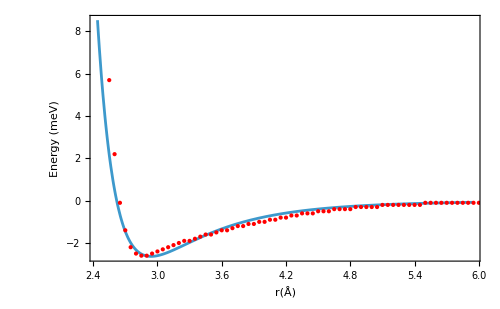

```mathematica
min=x/.FindMinimum[nlmLJ[x],{x,3}][[2]];
Plot[nlmLJ[x],{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500


]
```

```mathematica
Mm=ϵ(Exp[(-2 (x-x0))/b]-2 Exp[(-(x-x0))/b]);
```

```mathematica
nlmM = NonlinearModelFit[dataNEW2[atom],Mm,{b,ϵ,x0},x,MaxIterations->Infinity]
```

FittedModel[…]

```mathematica
nlmM["RSquared"]
```

0.991997

```mathematica
nlmM["BestFitParameters"]
```

{b→0.704843,ϵ→2.34744,x0→2.94367}

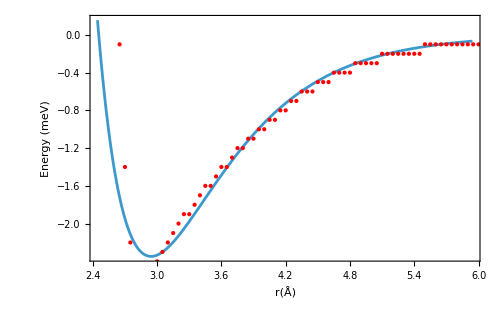

```mathematica
min=x/.FindMinimum[nlmM[x],{x,3}][[2]];
Plot[nlmM[x],{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500


]
```

```mathematica
inter = Interpolation[dataNEW[atom]]
```

InterpolatingFunction[…]

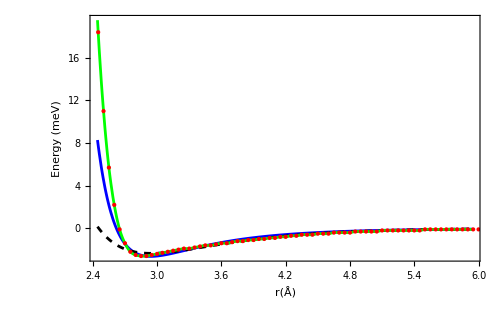

```mathematica
Plot[{nlmLJ[x],nlmM[x],inter[x]},{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500,
PlotStyle->{Blue,{Black,Dashed},Green}

]
```

Let' s compare the prediction of the a_0 (molecule length) of DFTB+ VS LJ vs M potentials:

```mathematica
{{"LJP",x/.FindMinimum[nlmLJ[x],{x,3}][[2]]},
{"MP",x/.FindMinimum[nlmM[x],{x,3}][[2]]},
{"DFTB+",x/.FindMinimum[inter[x],{x,3}][[2]]}
}//TableForm
```

InterpolatingFunction::dmval: Input value {1.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

LJP | 2.94058
MP | 2.94367
DFTB+ | 2.875

Let’s compute the strength of the DFTB+ computed potential, this is the u’’(x)

```mathematica
D[inter[x],{x,2}]/.Solve[D[inter[x],x]==0,x][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

40.

The strenght of the potential is related with the spring constant,

## Ne_2

```mathematica
atom = "Ne";
file = "results-"<>atom<>".dat";
data[atom]=Import[file];
ListPlot[data[atom][[1;;-2]],PlotRange->All]
```

-Graphics-

```mathematica
dataNEW[atom]=data[atom][[1;;-2]]//Map[(#-{0,data[atom][[-1,2]]}){1,10^3}&,#]&;
dataNEW[atom]//ListPlot[#,PlotRange->All]&
```

-Graphics-

```mathematica
LJm = 4 ϵ ((a/x)^12-(a/x)^6)  ;
```

```mathematica
nlmLJ = NonlinearModelFit[dataNEW[atom],LJm,{a,ϵ},x,MaxIterations->Infinity]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[…]

```mathematica
nlmLJ[x]
```

-1.09855×10^12 ((3.02167×10^-18)/x^12-(1.7383×10^-9)/x^6)

```mathematica
nlmLJ["RSquared"]
```

0.342408

```mathematica
nlmLJ["BestFitParameters"]
```

{a→0.0346753,ϵ→-2.74637×10^11}

```mathematica
Show[ListPlot[dataNEW[atom]],Plot[nlm[x],{x,0,7}],Frame->True]
```

-Graphics-

We can see that it is not a good model

```mathematica
dataNEW2[atom]=dataNEW[atom][[7;;-1]]
```

{{2.7,-1.4},{2.75,-2.2},{2.8,-2.5},{2.85,-2.6},{2.9,-2.6},{2.95,-2.5},{3.,-2.4},{3.05,-2.3},{3.1,-2.2},{3.15,-2.1},{3.2,-2.},{3.25,-1.9},{3.3,-1.9},{3.35,-1.8},{3.4,-1.7},{3.45,-1.6},{3.5,-1.6},{3.55,-1.5},{3.6,-1.4},{3.65,-1.4},{3.7,-1.3},{3.75,-1.2},{3.8,-1.2},{3.85,-1.1},{3.9,-1.1},{3.95,-1.},{4.,-1.},{4.05,-0.9},{4.1,-0.9},{4.15,-0.8},{4.2,-0.8},{4.25,-0.7},{4.3,-0.7},{4.35,-0.6},{4.4,-0.6},{4.45,-0.6},{4.5,-0.5},{4.55,-0.5},{4.6,-0.5},{4.65,-0.4},{4.7,-0.4},{4.75,-0.4},{4.8,-0.4},{4.85,-0.3},{4.9,-0.3},{4.95,-0.3},{5.,-0.3},{5.05,-0.3},{5.1,-0.2},{5.15,-0.2},{5.2,-0.2},{5.25,-0.2},{5.3,-0.2},{5.35,-0.2},{5.4,-0.2},{5.45,-0.2},{5.5,-0.1},{5.55,-0.1},{5.6,-0.1},{5.65,-0.1},{5.7,-0.1},{5.75,-0.1},{5.8,-0.1},{5.85,-0.1},{5.9,-0.1},{5.95,-0.1},{6.,-0.1},{6.05,-0.1},{6.1,-0.1},{6.15,-0.1},{6.2,-0.1},{6.25,0.},{6.3,0.},{6.35,0.},{6.4,0.},{6.45,0.},{6.5,0.},{6.55,0.},{6.6,0.},{6.65,0.},{6.7,0.},{6.75,0.},{6.8,0.},{6.85,0.},{6.9,0.},{6.95,0.},{7.,0.}}

```mathematica
LJm = 4 ϵ ((a/x)^12-(a/x)^6)  ;
```

```mathematica
nlmLJ = NonlinearModelFit[dataNEW2[atom],LJm,{a,ϵ},x,MaxIterations->Infinity]
```

FittedModel[…]

```mathematica
nlmLJ[x]
```

10.5322 (104505./x^12-323.272/x^6)

```mathematica
nlmLJ["RSquared"]
```

0.988291

```mathematica
nlmLJ["BestFitParameters"]
```

{a→2.61976,ϵ→2.63305}

```mathematica
min=x/.FindMinimum[nlmLJ[x],{x,3}][[2]];
Plot[nlmLJ[x],{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500


]
```

-Graphics-

```mathematica
Mm=ϵ(Exp[(-2 (x-x0))/b]-2 Exp[(-(x-x0))/b]);
```

```mathematica
nlmM = NonlinearModelFit[dataNEW2[atom],Mm,{b,ϵ,x0},x,MaxIterations->Infinity]
```

FittedModel[…]

```mathematica
nlmM["RSquared"]
```

0.991997

```mathematica
nlmM["BestFitParameters"]
```

{b→0.704843,ϵ→2.34744,x0→2.94367}

```mathematica
min=x/.FindMinimum[nlmM[x],{x,3}][[2]];
Plot[nlmM[x],{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500


]
```

-Graphics-

```mathematica
inter = Interpolation[dataNEW[atom]]
```

InterpolatingFunction[…]

```mathematica
Plot[{nlmLJ[x],nlmM[x],inter[x]},{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500,
PlotStyle->{Blue,{Black,Dashed},Green}

]
```

-Graphics-

Let' s compare the prediction of the a_0 (molecule length) of DFTB+ VS LJ vs M potentials:

```mathematica
{{"LJP",x/.FindMinimum[nlmLJ[x],{x,3}][[2]]},
{"MP",x/.FindMinimum[nlmM[x],{x,3}][[2]]},
{"DFTB+",x/.FindMinimum[inter[x],{x,3}][[2]]}
}//TableForm
```

InterpolatingFunction::dmval: Input value {1.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

LJP | 2.94058
MP | 2.94367
DFTB+ | 2.875

Let’s compute the strength of the DFTB+ computed potential, this is the u’’(x)

```mathematica
D[inter[x],{x,2}]/.Solve[D[inter[x],x]==0,x][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

40.

The strenght of the potential is related with the spring constant,

## Ar_2

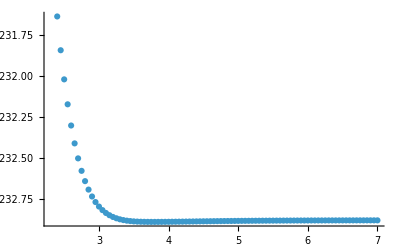

```mathematica
atom = "Ar";
file = "results-"<>atom<>".dat";
data[atom]=Import[file];
ListPlot[data[atom][[1;;-2]],PlotRange->All]
```

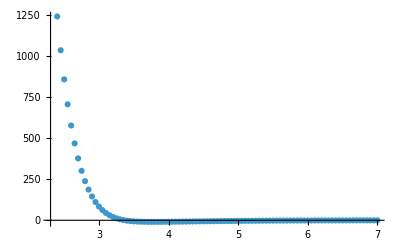

```mathematica
dataNEW[atom]=data[atom][[1;;-2]]//Map[(#-{0,data[atom][[-1,2]]}){1,10^3}&,#]&;
dataNEW[atom]//ListPlot[#,PlotRange->All]&
```

```mathematica
LJm = 4 ϵ ((a/x)^12-(a/x)^6)  ;
```

```mathematica
nlmLJ = NonlinearModelFit[dataNEW[atom],LJm,{a,ϵ},x,MaxIterations->Infinity]
```

FittedModel[…]

```mathematica
nlmLJ[x]
```

-1.55884×10^14 ((1.29394×10^-18)/x^12-(1.13752×10^-9)/x^6)

```mathematica
nlmLJ["RSquared"]
```

0.883891

```mathematica
nlmLJ["BestFitParameters"]
```

{a→0.0323092,ϵ→-3.8971×10^13}

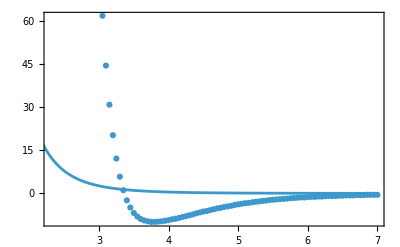

```mathematica
Show[ListPlot[dataNEW[atom]],Plot[nlm[x],{x,0,7}],Frame->True]
```

We can see that it is not a good model

```mathematica
dataNEW2[atom]=dataNEW[atom][[17;;-1]]
```

{{3.2,20.2},{3.25,12.1},{3.3,5.8},{3.35,1.1},{3.4,-2.4},{3.45,-4.9},{3.5,-6.8},{3.55,-8.},{3.6,-8.9},{3.65,-9.4},{3.7,-9.7},{3.75,-9.9},{3.8,-9.9},{3.85,-9.8},{3.9,-9.7},{3.95,-9.5},{4.,-9.3},{4.05,-9.},{4.1,-8.8},{4.15,-8.5},{4.2,-8.2},{4.25,-7.9},{4.3,-7.6},{4.35,-7.3},{4.4,-6.9},{4.45,-6.6},{4.5,-6.3},{4.55,-6.1},{4.6,-5.8},{4.65,-5.5},{4.7,-5.2},{4.75,-5.},{4.8,-4.7},{4.85,-4.5},{4.9,-4.3},{4.95,-4.},{5.,-3.8},{5.05,-3.6},{5.1,-3.4},{5.15,-3.3},{5.2,-3.1},{5.25,-2.9},{5.3,-2.8},{5.35,-2.6},{5.4,-2.5},{5.45,-2.3},{5.5,-2.2},{5.55,-2.1},{5.6,-2.},{5.65,-1.9},{5.7,-1.8},{5.75,-1.7},{5.8,-1.6},{5.85,-1.5},{5.9,-1.4},{5.95,-1.4},{6.,-1.3},{6.05,-1.2},{6.1,-1.2},{6.15,-1.1},{6.2,-1.1},{6.25,-1.},{6.3,-0.9},{6.35,-0.9},{6.4,-0.9},{6.45,-0.8},{6.5,-0.8},{6.55,-0.7},{6.6,-0.7},{6.65,-0.7},{6.7,-0.6},{6.75,-0.6},{6.8,-0.6},{6.85,-0.5},{6.9,-0.5},{6.95,-0.5},{7.,-0.5}}

```mathematica
LJm = 4 ϵ ((a/x)^12-(a/x)^6)  ;
```

```mathematica
nlmLJ = NonlinearModelFit[dataNEW2[atom],LJm,{a,ϵ},x,MaxIterations->Infinity]
```

FittedModel[…]

```mathematica
nlmLJ[x]
```

41.416 ((2.12653×10^6)/x^12-1458.26/x^6)

```mathematica
nlmLJ["RSquared"]
```

0.998426

```mathematica
nlmLJ["BestFitParameters"]
```

{a→3.36749,ϵ→10.354}

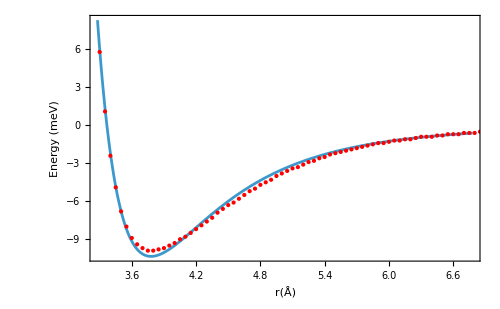

```mathematica
min=x/.FindMinimum[nlmLJ[x],{x,3}][[2]];
Plot[nlmLJ[x],{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500


]
```

```mathematica
Mm=ϵ(Exp[(-2 (x-x0))/b]-2 Exp[(-(x-x0))/b]);
```

```mathematica
nlmM = NonlinearModelFit[dataNEW2[atom],Mm,{b,ϵ,x0},x,MaxIterations->Infinity]
```

FittedModel[…]

```mathematica
nlmM["RSquared"]
```

0.988799

```mathematica
nlmM["BestFitParameters"]
```

{b→0.658307,ϵ→10.6402,x0→3.83972}

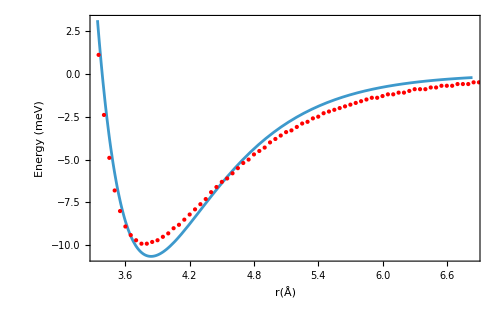

```mathematica
min=x/.FindMinimum[nlmM[x],{x,3}][[2]];
Plot[nlmM[x],{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500


]
```

```mathematica
inter = Interpolation[dataNEW[atom]]
```

InterpolatingFunction[…]

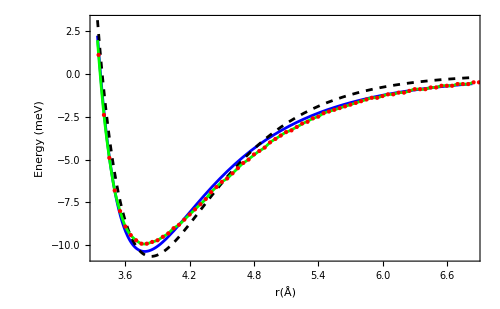

```mathematica
Plot[{nlmLJ[x],nlmM[x],inter[x]},{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500,
PlotStyle->{Blue,{Black,Dashed},Green}

]
```

Let' s compare the prediction of the a_0 (molecule length) of DFTB+ VS LJ vs M potentials:

```mathematica
{{"LJP",x/.FindMinimum[nlmLJ[x],{x,3}][[2]]},
{"MP",x/.FindMinimum[nlmM[x],{x,3}][[2]]},
{"DFTB+",x/.FindMinimum[inter[x],{x,3}][[2]]}
}//TableForm
```

InterpolatingFunction::dmval: Input value {-10.4301} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

LJP | 3.77988
MP | 3.83972
DFTB+ | 3.77362

Let’s compute the strength of the DFTB+ computed potential, this is the u’’(x)

```mathematica
D[inter[x],{x,2}]/.Solve[D[inter[x],x]==0,x][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

61.101

The strenght of the potential is related with the spring constant, here it is in units of meV/Å^2

## Kr_2

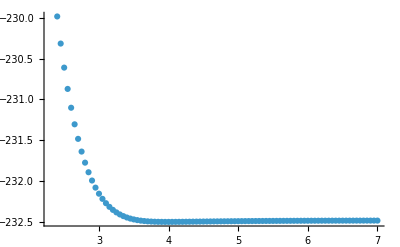

```mathematica
atom = "Kr";
file = "results-"<>atom<>".dat";
data[atom]=Import[file];
ListPlot[data[atom][[1;;-2]],PlotRange->All]
```

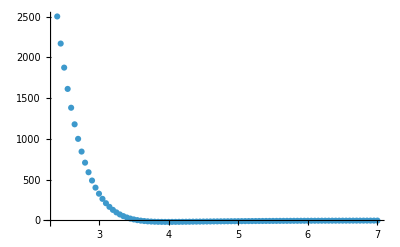

```mathematica
dataNEW[atom]=data[atom][[1;;-2]]//Map[(#-{0,data[atom][[-1,2]]}){1,10^3}&,#]&;
dataNEW[atom]//ListPlot[#,PlotRange->All]&
```

```mathematica
LJm = 4 ϵ ((a/x)^12-(a/x)^6)  ;
```

```mathematica
nlmLJ = NonlinearModelFit[dataNEW[atom],LJm,{a,ϵ},x,MaxIterations->Infinity]
```

FittedModel[…]

```mathematica
nlmLJ[x]
```

-3.59328×10^14 ((1.28908×10^-18)/x^12-(1.13538×10^-9)/x^6)

```mathematica
nlmLJ["RSquared"]
```

0.941154

```mathematica
nlmLJ["BestFitParameters"]
```

{a→0.0322991,ϵ→-8.9832×10^13}

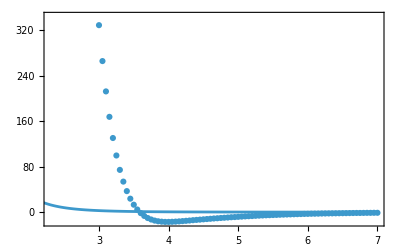

```mathematica
Show[ListPlot[dataNEW[atom]],Plot[nlm[x],{x,0,7}],Frame->True]
```

We can see that it is not a good model

```mathematica
dataNEW2[atom]=dataNEW[atom][[21;;-1]]
```

{{3.4,36.9},{3.45,23.6},{3.5,13.},{3.55,4.6},{3.6,-1.8},{3.65,-6.7},{3.7,-10.4},{3.75,-13.},{3.8,-14.9},{3.85,-16.1},{3.9,-16.8},{3.95,-17.2},{4.,-17.2},{4.05,-17.},{4.1,-16.7},{4.15,-16.3},{4.2,-15.8},{4.25,-15.3},{4.3,-14.8},{4.35,-14.2},{4.4,-13.7},{4.45,-13.2},{4.5,-12.7},{4.55,-12.2},{4.6,-11.7},{4.65,-11.2},{4.7,-10.8},{4.75,-10.3},{4.8,-9.9},{4.85,-9.5},{4.9,-9.},{4.95,-8.7},{5.,-8.3},{5.05,-7.9},{5.1,-7.5},{5.15,-7.2},{5.2,-6.9},{5.25,-6.5},{5.3,-6.2},{5.35,-5.9},{5.4,-5.6},{5.45,-5.4},{5.5,-5.1},{5.55,-4.9},{5.6,-4.6},{5.65,-4.4},{5.7,-4.2},{5.75,-4.},{5.8,-3.8},{5.85,-3.6},{5.9,-3.4},{5.95,-3.2},{6.,-3.1},{6.05,-2.9},{6.1,-2.8},{6.15,-2.7},{6.2,-2.5},{6.25,-2.4},{6.3,-2.3},{6.35,-2.2},{6.4,-2.1},{6.45,-2.},{6.5,-1.9},{6.55,-1.8},{6.6,-1.7},{6.65,-1.6},{6.7,-1.5},{6.75,-1.5},{6.8,-1.4},{6.85,-1.3},{6.9,-1.3},{6.95,-1.2},{7.,-1.2}}

```mathematica
LJm = 4 ϵ ((a/x)^12-(a/x)^6)  ;
```

```mathematica
nlmLJ = NonlinearModelFit[dataNEW2[atom],LJm,{a,ϵ},x,MaxIterations->Infinity]
```

FittedModel[…]

```mathematica
nlmLJ[x]
```

69.0348 ((4.54999×10^6)/x^12-2133.07/x^6)

```mathematica
nlmLJ["RSquared"]
```

0.999082

```mathematica
nlmLJ["BestFitParameters"]
```

{a→3.58785,ϵ→17.2587}

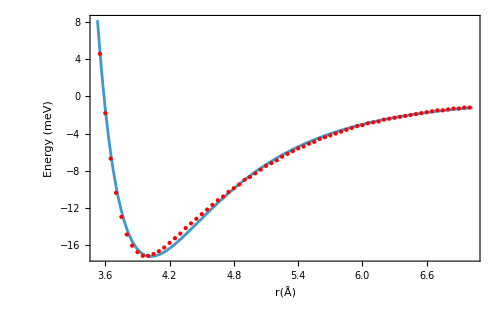

```mathematica
min=x/.FindMinimum[nlmLJ[x],{x,3}][[2]];
Plot[nlmLJ[x],{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500


]
```

```mathematica
Mm=ϵ(Exp[(-2 (x-x0))/b]-2 Exp[(-(x-x0))/b]);
```

```mathematica
nlmM = NonlinearModelFit[dataNEW2[atom],Mm,{b,ϵ,x0},x,MaxIterations->Infinity]
```

FittedModel[…]

```mathematica
nlmM["RSquared"]
```

0.988325

```mathematica
nlmM["BestFitParameters"]
```

{b→0.665186,ϵ→18.0285,x0→4.06071}

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

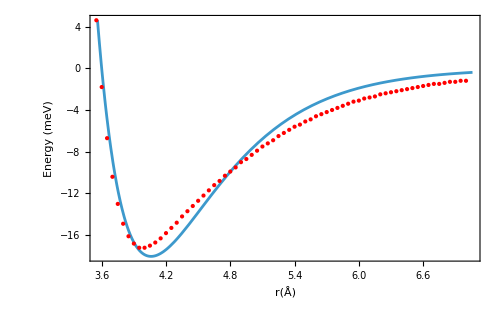

```mathematica
min=x/.FindMinimum[nlmM[x],{x,3}][[2]];
Plot[nlmM[x],{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500


]
```

```mathematica
inter = Interpolation[dataNEW[atom]]
```

InterpolatingFunction[…]

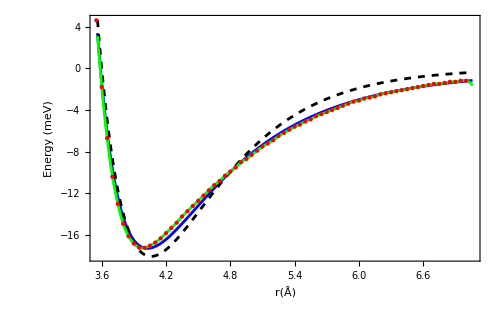

```mathematica
Plot[{nlmLJ[x],nlmM[x],inter[x]},{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500,
PlotStyle->{Blue,{Black,Dashed},Green}

]
```

Let' s compare the prediction of the a_0 (molecule length) of DFTB+ VS LJ vs M potentials:

```mathematica
{{"LJP",x/.FindMinimum[nlmLJ[x],{x,3}][[2]]},
{"MP",x/.FindMinimum[nlmM[x],{x,3}][[2]]},
{"DFTB+",x/.FindMinimum[inter[x],{x,3}][[2]]}
}//TableForm
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {-7.60556} lies outside the range of data in the interpolating function. Extrapolation will be used.

LJP | 4.02722
MP | 4.06071
DFTB+ | 3.97362

Let’s compute the strength of the DFTB+ computed potential, this is the u’’(x)

```mathematica
D[inter[x],{x,2}]/.Solve[D[inter[x],x]==0,x][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

122.202

The strenght of the potential is related with the spring constant, here it is in units of meV/Å^2

## Xe_2

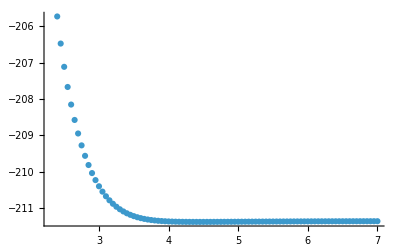

```mathematica
atom = "Xe";
file = "results-"<>atom<>".dat";
data[atom]=Import[file];
ListPlot[data[atom][[1;;-2]],PlotRange->All]
```

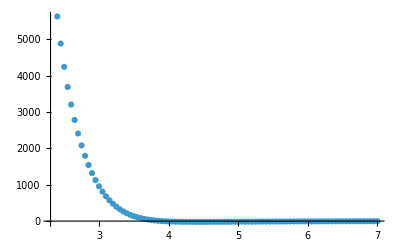

```mathematica
dataNEW[atom]=data[atom][[1;;-2]]//Map[(#-{0,data[atom][[-1,2]]}){1,10^3}&,#]&;
dataNEW[atom]//ListPlot[#,PlotRange->All]&
```

```mathematica
LJm = 4 ϵ ((a/x)^12-(a/x)^6)  ;
```

```mathematica
nlmLJ = NonlinearModelFit[dataNEW[atom],LJm,{a,ϵ},x,MaxIterations->Infinity]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[…]

```mathematica
nlmLJ[x]
```

-9.2637×10^14 ((1.06976×10^-18)/x^12-(1.03429×10^-9)/x^6)

```mathematica
nlmLJ["RSquared"]
```

0.966406

```mathematica
nlmLJ["BestFitParameters"]
```

{a→0.031801,ϵ→-2.31592×10^14}

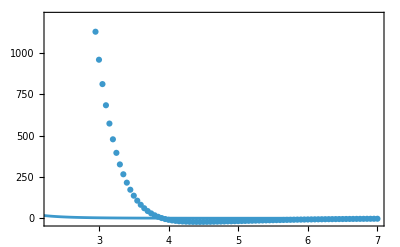

```mathematica
Show[ListPlot[dataNEW[atom]],Plot[nlm[x],{x,0,7}],Frame->True]
```

We can see that it is not a good model

```mathematica
dataNEW2[atom]=dataNEW[atom][[27;;-1]]
```

{{3.7,43.3},{3.75,29.3},{3.8,17.8},{3.85,8.6},{3.9,1.1},{3.95,-4.8},{4.,-9.5},{4.05,-13.1},{4.1,-15.9},{4.15,-18.1},{4.2,-19.6},{4.25,-20.7},{4.3,-21.4},{4.35,-21.9},{4.4,-22.1},{4.45,-22.1},{4.5,-22.},{4.55,-21.7},{4.6,-21.4},{4.65,-21.},{4.7,-20.6},{4.75,-20.1},{4.8,-19.6},{4.85,-19.},{4.9,-18.5},{4.95,-17.9},{5.,-17.3},{5.05,-16.8},{5.1,-16.2},{5.15,-15.6},{5.2,-15.1},{5.25,-14.5},{5.3,-14.},{5.35,-13.4},{5.4,-12.9},{5.45,-12.4},{5.5,-11.9},{5.55,-11.4},{5.6,-10.9},{5.65,-10.5},{5.7,-10.},{5.75,-9.6},{5.8,-9.2},{5.85,-8.7},{5.9,-8.4},{5.95,-8.},{6.,-7.6},{6.05,-7.3},{6.1,-6.9},{6.15,-6.6},{6.2,-6.3},{6.25,-6.},{6.3,-5.7},{6.35,-5.5},{6.4,-5.2},{6.45,-5.},{6.5,-4.8},{6.55,-4.5},{6.6,-4.3},{6.65,-4.1},{6.7,-3.9},{6.75,-3.7},{6.8,-3.6},{6.85,-3.4},{6.9,-3.3},{6.95,-3.1},{7.,-3.}}

```mathematica
LJm = 4 ϵ ((a/x)^12-(a/x)^6)  ;
```

```mathematica
nlmLJ = NonlinearModelFit[dataNEW2[atom],LJm,{a,ϵ},x,MaxIterations->Infinity]
```

FittedModel[…]

```mathematica
nlmLJ[x]
```

92.0094 ((1.23566×10^7)/x^12-3515.2/x^6)

```mathematica
nlmLJ["RSquared"]
```

0.992933

```mathematica
nlmLJ["BestFitParameters"]
```

{a→3.89934,ϵ→23.0024}

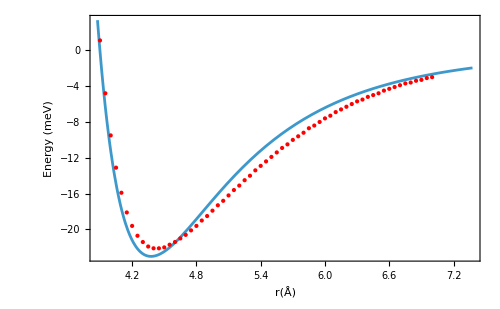

```mathematica
min=x/.FindMinimum[nlmLJ[x],{x,3}][[2]];
Plot[nlmLJ[x],{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500


]
```

```mathematica
Mm=ϵ(Exp[(-2 (x-x0))/b]-2 Exp[(-(x-x0))/b]);
```

```mathematica
nlmM = NonlinearModelFit[dataNEW2[atom],Mm,{b,ϵ,x0},x,MaxIterations->Infinity]
```

FittedModel[…]

```mathematica
nlmM["RSquared"]
```

0.994115

```mathematica
nlmM["BestFitParameters"]
```

{b→0.807252,ϵ→23.3156,x0→4.48497}

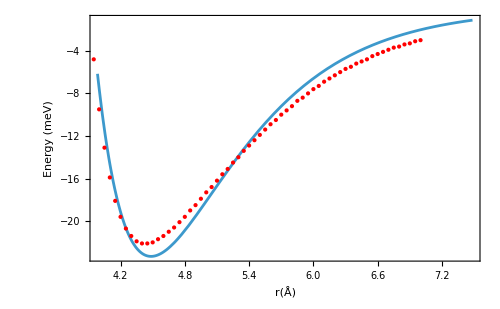

```mathematica
min=x/.FindMinimum[nlmM[x],{x,3}][[2]];
Plot[nlmM[x],{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500


]
```

```mathematica
inter = Interpolation[dataNEW[atom]]
```

InterpolatingFunction[…]

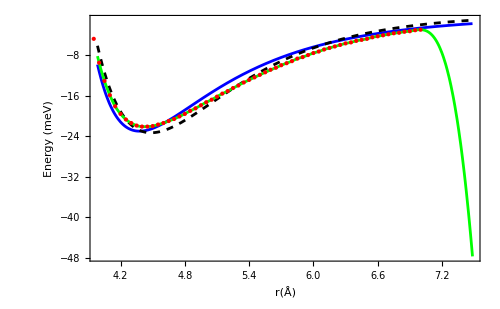

```mathematica
Plot[{nlmLJ[x],nlmM[x],inter[x]},{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500,
PlotStyle->{Blue,{Black,Dashed},Green}

]
```

Let' s compare the prediction of the a_0 (molecule length) of DFTB+ VS LJ vs M potentials:

```mathematica
{{"LJP",x/.FindMinimum[nlmLJ[x],{x,3}][[2]]},
{"MP",x/.FindMinimum[nlmM[x],{x,3}][[2]]},
{"DFTB+",x/.FindMinimum[inter[x],{x,3}][[2]]}
}//TableForm
```

LJP | 4.37687
MP | 4.48497
DFTB+ | 4.42362

Let’s compute the strength of the DFTB+ computed potential, this is the u’’(x)

```mathematica
D[inter[x],{x,2}]/.Solve[D[inter[x],x]==0,x][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

61.101

The strenght of the potential is related with the spring constant, here it is in units of meV/Å^2

## Rn_2

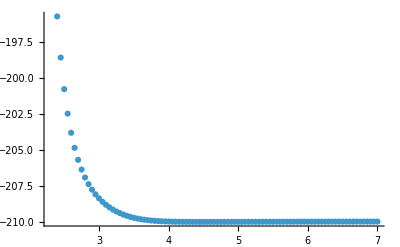

```mathematica
atom = "Rn";
file = "results-"<>atom<>".dat";
data[atom]=Import[file];
ListPlot[data[atom][[1;;-2]],PlotRange->All]
```

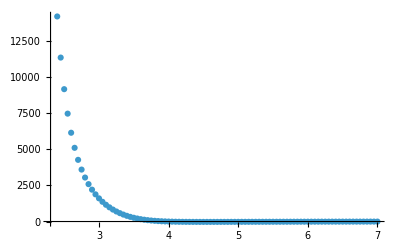

```mathematica
dataNEW[atom]=data[atom][[1;;-2]]//Map[(#-{0,data[atom][[-1,2]]}){1,10^3}&,#]&;
dataNEW[atom]//ListPlot[#,PlotRange->All]&
```

```mathematica
LJm = 4 ϵ ((a/x)^12-(a/x)^6)  ;
```

```mathematica
nlmLJ = NonlinearModelFit[dataNEW[atom],LJm,{a,ϵ},x,MaxIterations->Infinity]
```

FittedModel[…]

```mathematica
nlmLJ[x]
```

-1.88033×10^15 ((1.17418×10^-18)/x^12-(1.08359×10^-9)/x^6)

```mathematica
nlmLJ["RSquared"]
```

0.926742

```mathematica
nlmLJ["BestFitParameters"]
```

{a→0.0320488,ϵ→-4.70082×10^14}

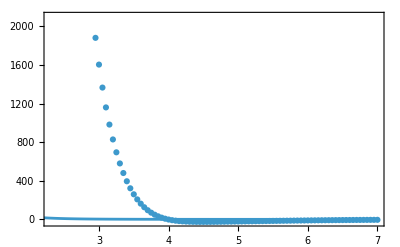

```mathematica
Show[ListPlot[dataNEW[atom]],Plot[nlm[x],{x,0,7}],Frame->True]
```

We can see that it is not a good model

```mathematica
dataNEW2[atom]=dataNEW[atom][[28;;-1]]
```

{{3.75,69.3},{3.8,48.4},{3.85,31.4},{3.9,17.7},{3.95,6.8},{4.,-1.9},{4.05,-8.7},{4.1,-13.9},{4.15,-17.8},{4.2,-20.8},{4.25,-22.9},{4.3,-24.4},{4.35,-25.4},{4.4,-26.1},{4.45,-26.4},{4.5,-26.4},{4.55,-26.3},{4.6,-26.1},{4.65,-25.8},{4.7,-25.4},{4.75,-24.9},{4.8,-24.4},{4.85,-23.9},{4.9,-23.3},{4.95,-22.8},{5.,-22.2},{5.05,-21.6},{5.1,-21.},{5.15,-20.4},{5.2,-19.9},{5.25,-19.3},{5.3,-18.7},{5.35,-18.1},{5.4,-17.5},{5.45,-17.},{5.5,-16.4},{5.55,-15.9},{5.6,-15.3},{5.65,-14.8},{5.7,-14.3},{5.75,-13.8},{5.8,-13.2},{5.85,-12.7},{5.9,-12.3},{5.95,-11.8},{6.,-11.3},{6.05,-10.9},{6.1,-10.5},{6.15,-10.},{6.2,-9.6},{6.25,-9.2},{6.3,-8.8},{6.35,-8.5},{6.4,-8.1},{6.45,-7.8},{6.5,-7.4},{6.55,-7.1},{6.6,-6.8},{6.65,-6.5},{6.7,-6.2},{6.75,-6.},{6.8,-5.7},{6.85,-5.5},{6.9,-5.2},{6.95,-5.},{7.,-4.8}}

```mathematica
LJm = 4 ϵ ((a/x)^12-(a/x)^6)  ;
```

```mathematica
nlmLJ = NonlinearModelFit[dataNEW2[atom],LJm,{a,ϵ},x,MaxIterations->Infinity]
```

FittedModel[…]

```mathematica
nlmLJ[x]
```

113.084 ((1.60318×10^7)/x^12-4003.97/x^6)

```mathematica
nlmLJ["RSquared"]
```

0.992117

```mathematica
nlmLJ["BestFitParameters"]
```

{a→3.98488,ϵ→28.2711}

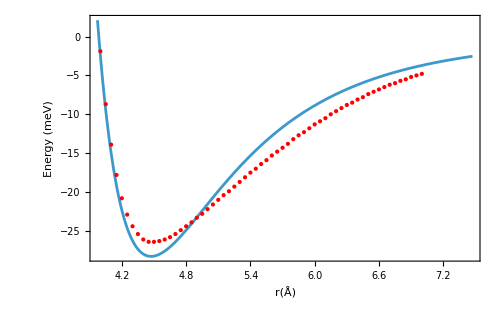

```mathematica
min=x/.FindMinimum[nlmLJ[x],{x,3}][[2]];
Plot[nlmLJ[x],{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500


]
```

```mathematica
Mm=ϵ(Exp[(-2 (x-x0))/b]-2 Exp[(-(x-x0))/b]);
```

```mathematica
nlmM = NonlinearModelFit[dataNEW2[atom],Mm,{b,ϵ,x0},x,MaxIterations->Infinity]
```

FittedModel[…]

```mathematica
nlmM["RSquared"]
```

0.98635

```mathematica
nlmM["BestFitParameters"]
```

{b→0.810513,ϵ→29.0089,x0→4.57707}

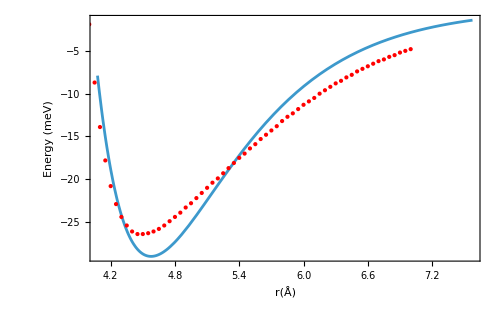

```mathematica
min=x/.FindMinimum[nlmM[x],{x,3}][[2]];
Plot[nlmM[x],{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500


]
```

```mathematica
inter = Interpolation[dataNEW[atom]]
```

InterpolatingFunction[…]

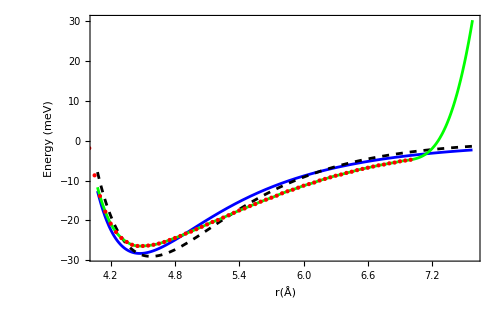

```mathematica
Plot[{nlmLJ[x],nlmM[x],inter[x]},{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500,
PlotStyle->{Blue,{Black,Dashed},Green}

]
```

Let' s compare the prediction of the a_0 (molecule length) of DFTB+ VS LJ vs M potentials:

```mathematica
{{"LJP",x/.FindMinimum[nlmLJ[x],{x,3}][[2]]},
{"MP",x/.FindMinimum[nlmM[x],{x,3}][[2]]},
{"DFTB+",x/.FindMinimum[inter[x],{x,3}][[2]]}
}//TableForm
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

LJP | 4.47288
MP | 4.57707
DFTB+ | 4.47296

Let’s compute the strength of the DFTB+ computed potential, this is the u’’(x)

```mathematica
D[inter[x],{x,2}]/.Solve[D[inter[x],x]==0,x][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

83.2666

The strenght of the potential is related with the spring constant, here it is in units of meV/Å^2

## The N_2 and O_2 molecules

```mathematica
Range[0.4,6.0,0.05]//Map[ToString[NumberForm[#,{4,2}]]<>" "&,#]&//StringJoin
```

0.40 0.45 0.50 0.55 0.60 0.65 0.70 0.75 0.80 0.85 0.90 0.95 1.00 1.05 1.10 1.15 1.20 1.25 1.30 1.35 1.40 1.45 1.50 1.55 1.60 1.65 1.70 1.75 1.80 1.85 1.90 1.95 2.00 2.05 2.10 2.15 2.20 2.25 2.30 2.35 2.40 2.45 2.50 2.55 2.60 2.65 2.70 2.75 2.80 2.85 2.90 2.95 3.00 3.05 3.10 3.15 3.20 3.25 3.30 3.35 3.40 3.45 3.50 3.55 3.60 3.65 3.70 3.75 3.80 3.85 3.90 3.95 4.00 4.05 4.10 4.15 4.20 4.25 4.30 4.35 4.40 4.45 4.50 4.55 4.60 4.65 4.70 4.75 4.80 4.85 4.90 4.95 5.00 5.05 5.10 5.15 5.20 5.25 5.30 5.35 5.40 5.45 5.50 5.55 5.60 5.65 5.70 5.75 5.80 5.85 5.90 5.95 6.00

## N

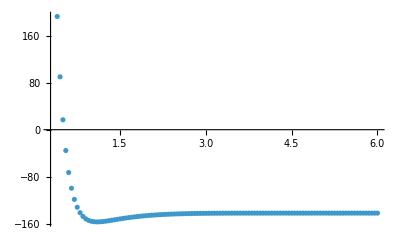

```mathematica
atom = "N";
file = "results-"<>atom<>".dat";
data[atom]=Import[file];
ListPlot[data[atom][[1;;-2]],PlotRange->All]
```

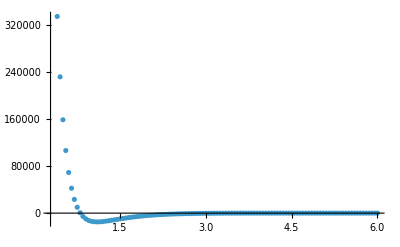

```mathematica
dataNEW[atom]=data[atom][[1;;-2]]//Map[(#-{0,data[atom][[-1,2]]}){1,10^3}&,#]&;
dataNEW[atom]//ListPlot[#,PlotRange->All]&
```

```mathematica
LJm = 4 ϵ ((a/x)^12-(a/x)^6)  ;
```

```mathematica
nlmLJ = NonlinearModelFit[dataNEW[atom],LJm,{a,ϵ},x,MaxIterations->Infinity]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[…]

```mathematica
nlmLJ[x]
```

3.39311×10^-17 ((1.881×10^17)/x^12-(4.33704×10^8)/x^6)

```mathematica
nlmLJ["RSquared"]
```

0.726102

```mathematica
nlmLJ["BestFitParameters"]
```

{a→27.5126,ϵ→8.48278×10^-18}

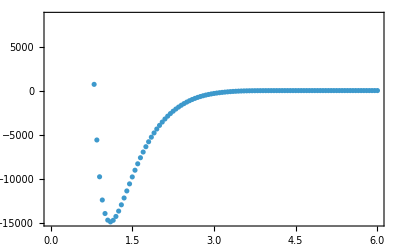

```mathematica
Show[ListPlot[dataNEW[atom]],Plot[nlm[x],{x,0,7}],Frame->True]
```

We can see that it is not a good model

```mathematica
dataNEW2[atom]=dataNEW[atom][[9;;-1]]
```

{{0.8,706.},{0.85,-5615.1},{0.9,-9794.9},{0.95,-12433.2},{1.,-13968.2},{1.05,-14719.8},{1.1,-14920.7},{1.15,-14740.4},{1.2,-14301.5},{1.25,-13692.8},{1.3,-12978.5},{1.35,-12204.5},{1.4,-11404.},{1.45,-10600.8},{1.5,-9811.8},{1.55,-9048.8},{1.6,-8319.8},{1.65,-7630.2},{1.7,-6982.6},{1.75,-6378.},{1.8,-5816.},{1.85,-5295.1},{1.9,-4813.3},{1.95,-4368.3},{2.,-3957.5},{2.05,-3578.6},{2.1,-3229.3},{2.15,-2907.9},{2.2,-2613.2},{2.25,-2343.6},{2.3,-2097.3},{2.35,-1872.3},{2.4,-1666.9},{2.45,-1479.4},{2.5,-1308.8},{2.55,-1154.},{2.6,-1014.3},{2.65,-888.8},{2.7,-776.8},{2.75,-677.2},{2.8,-589.},{2.85,-511.3},{2.9,-442.8},{2.95,-382.6},{3.,-329.7},{3.05,-283.2},{3.1,-242.2},{3.15,-206.1},{3.2,-174.},{3.25,-145.3},{3.3,-119.8},{3.35,-97.5},{3.4,-78.4},{3.45,-62.3},{3.5,-49.1},{3.55,-38.5},{3.6,-30.2},{3.65,-23.7},{3.7,-18.7},{3.75,-14.9},{3.8,-12.1},{3.85,-10.},{3.9,-8.3},{3.95,-7.1},{4.,-6.2},{4.05,-5.5},{4.1,-4.9},{4.15,-4.5},{4.2,-4.1},{4.25,-3.8},{4.3,-3.5},{4.35,-3.3},{4.4,-3.1},{4.45,-2.9},{4.5,-2.8},{4.55,-2.6},{4.6,-2.5},{4.65,-2.3},{4.7,-2.2},{4.75,-2.1},{4.8,-2.},{4.85,-1.9},{4.9,-1.8},{4.95,-1.7},{5.,-1.6},{5.05,-1.5},{5.1,-1.4},{5.15,-1.4},{5.2,-1.3},{5.25,-1.2},{5.3,-1.2},{5.35,-1.1},{5.4,-1.1},{5.45,-1.},{5.5,-1.},{5.55,-0.9},{5.6,-0.9},{5.65,-0.8},{5.7,-0.8},{5.75,-0.7},{5.8,-0.7},{5.85,-0.7},{5.9,-0.7},{5.95,-0.6},{6.,-0.6}}

```mathematica
LJm = 4 ϵ ((a/x)^12-(a/x)^6)  ;
```

```mathematica
nlmLJ = NonlinearModelFit[dataNEW2[atom],LJm,{a,ϵ},x,MaxIterations->Infinity]
```

FittedModel[…]

```mathematica
nlmLJ[x]
```

-2.74438 ((5.3507×10^-31)/x^12-(7.31485×10^-16)/x^6)

```mathematica
nlmLJ["RSquared"]
```

0.

```mathematica
nlmLJ["BestFitParameters"]
```

{a→-0.0030017,ϵ→-0.686094}

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

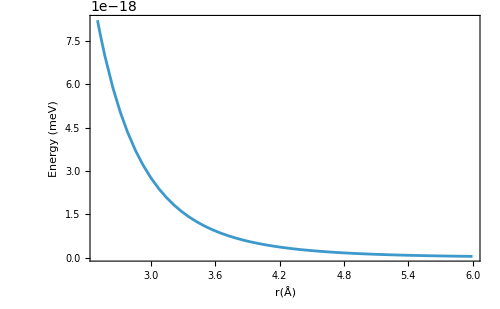

```mathematica
min=x/.FindMinimum[nlmLJ[x],{x,3}][[2]];
Plot[nlmLJ[x],{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500


]
```

```mathematica
Mm=ϵ(Exp[(-2 (x-x0))/b]-2 Exp[(-(x-x0))/b]);
```

```mathematica
nlmM = NonlinearModelFit[dataNEW2[atom],Mm,{b,ϵ,x0},x,MaxIterations->Infinity]
```

FittedModel[…]

```mathematica
nlmM["RSquared"]
```

0.9996

```mathematica
nlmM["BestFitParameters"]
```

{b→0.444848,ϵ→14984.8,x0→1.11064}

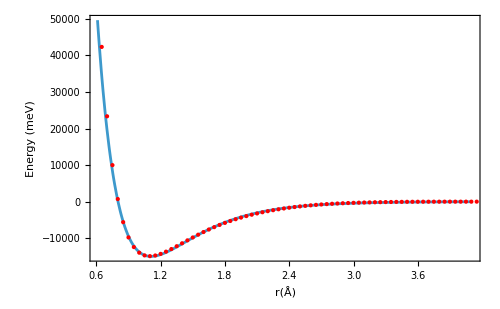

```mathematica
min=x/.FindMinimum[nlmM[x],{x,3}][[2]];
Plot[nlmM[x],{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500


]
```

```mathematica
inter = Interpolation[dataNEW[atom]]
```

InterpolatingFunction[…]

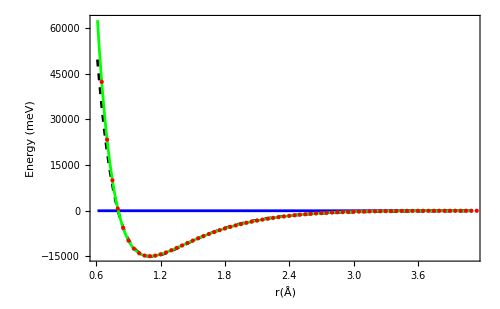

```mathematica
Plot[{nlmLJ[x],nlmM[x],inter[x]},{x,min-0.5,min+3},
Frame->True,
FrameLabel->{"r(Å)","Energy (meV)"},
PlotRange->All,
Epilog->{Red,Point[dataNEW[atom]]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->500,
PlotStyle->{Blue,{Black,Dashed},Green}

]
```

Let' s compare the prediction of the a_0 (molecule length) of DFTB+ VS LJ vs M potentials:

```mathematica
{{"LJP",x/.FindMinimum[nlmLJ[x],{x,3}][[2]]},
{"MP",x/.FindMinimum[nlmM[x],{x,3}][[2]]},
{"DFTB+",x/.FindMinimum[inter[x],{x,3}][[2]]}
}//TableForm
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

InterpolatingFunction::dmval: Input value {-4.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

LJP | 3.
MP | 1.11064
DFTB+ | 1.09767

Let’s compute the strength of the DFTB+ computed potential, this is the u’’(x)

```mathematica
D[inter[x],{x,2}]/.Solve[D[inter[x],x]==0,x][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

155640.

The strenght of the potential is related with the spring constant, here it is in units of meV/Å^2

THis is a covalent bonding that is why the strengh of the potential is high

Let’s compute the zero point energy (ZPE) for N_2 molecule. We can use the solution from the Schrodinguer equation

We need the reduced mass m of the  N_2

```mathematica
mN = 2.3259 10^6
```

2.3259×10^6